## Uvod v Mathematico, zaporedja in številske vrste

Dokument v programu Mathematica je razdeljen na celice, ki so ob desnem robu označene z oglatimi oklepaji. Delitev na celice je namenjena urejanju programa (pisava, kopiranje, združevanje več ukazov v celoto,...). Pri naših vajah so
  celice na sivem ozadju pojasnila,
  celice na zelenem ozadju naloge,
  celice na belem ozadju v okrepljeni pisavi so aktivni ukazi, ki jih program Mathematica izvrši.
Ko hočemo nek ukaz izvesti, se moramo s kurzorjem postaviti v celico, v kateri se ukaz nahaja, in pritisniti tipki Shift+Enter. Ob tem se izvedejo vsi ukazi, ki se nahajajo v dani celici. Program Mathematica lahko uporabljamo kot kalkulator.

1. Izračunajte naslednje izraze.
	a) 3 + 7
	b) (10 - 2)/5
	c) ln(1)
	d) sin(π/2)
	e) 2 √(3^2 + 4^2)
	f) ⅇ^0
	g) arcsin(1)

```mathematica
3+7
(10-2)/5
Log[1]
Sin[Pi/2]
2Sqrt[3^2+4^2]
E^0
ArcSin[1]
```

10

8/5

0

1

10

1

π/2

Ukazi in funkcije v programu Mathematica so ponavadi angleške besede za ta ukaz ali funkcijo, npr. Log za izračun naravnega logaritma, Sqrt za izračun kvadratnega korena ipd. Vsi vgrajeni ukazi in funkcije se začnejo z veliko začetnico. Če je ukaz sestavljen iz več besed, npr. ArcSin za arkus sinus, potem so besede ukaza napisane skupaj, vsaka pa se začne z veliko začetnico.

Oklepaji v Mathematici:
() Okrogle oklepaje uporabljamo kot običajno v aritmetičnih izrazih za spremembo vrstnega reda opracij: npr. 7*(5+3).
[] Oglate oklepaje uporabljamo za podajanje argumentov vseh ukazov in funkcij: npr. Sin[π] ali Expand[(x-1)(x+2)].
	Če ima ukaz več argumentov, jih ločimo z vejicami.
{} Zavite oklepaje uporabljamo za pisanje vektorjev, matrik, seznamov: npr. i⃗={1,0,0}.

V programu Mathematica lahko uporabljamo spremenljivke s poljubnimi imeni. Pri tem velja:
	- nekatera imena so rezervirana in jih Mathematica ne pusti spremeniti (npr. Pi, C, D, E).
	- kar začetnik pogosto spregleda je: xy NI produkt x*y, temveč spremenljivka xy.
Znak za množenje (*) lahko izpustimo, vendar ga je potrebno zamenjati s presledkom: x y = x*y .
  
Komentarje pišemo v oklepajih z zvezdico, npr. (* to je komentar *).

Izpis rezultata preprečimo s podpičjem na koncu ukaza.

Pomoč v Mathematici:
Ukaz ?ImeUkaza izpiše kratek opis uporabe ukaza. 
Sicer je na voljo tudi obširnejša pomoč, ki jo najdemo v meniju Help, ali s pritiskom na funkcijsko tipko F1.

Ukaz Clear[ ] izbriše vrednost, ki je prirejena dani spremenljivki.

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcTan[1];
```

```mathematica
(* pomoč za funkcijo sinus *)
?Sin
```

Realna števila v Mathematici:
Program Mathematica je orodje za simbolno računanje in vrača točne rezultate. Če želimo računati z realnimi števili, je potrebno število (tudi celo!) zapisati z decimalno PIKO! Mathematica računa v standardni IEEE aritmetiki. Vendar pa na zahtevo izračuna tudi več (ali manj) decimalk. Za izračun izraza na poljubno število decimalk uporabimo ukaz N[ ], kjer drugi argument poda število željenih števk (NE decimalnih mest). Če za celim številom pišemo ., ga Mathematica obravnava kot realno število.

2. a) Izračunajte število π na 50 decimalk natančno.
   b) Kako dober približek za število π je ulomek 22/7?
   c) Izračunajte kvadratni koren iz 1368.

```mathematica
N[Pi,51] 
N[Pi-22/7]
Sqrt[1368]
N[Sqrt[1368]]
Sqrt[1368.]
```

3.14159265358979323846264338327950288419716939937511

-0.00126449

6 √38

36.9865

36.9865

## Polinomi in racionalne funkcije

Ukaz Expand[ ] razširi produkt faktorjev v vsoto potenc.
Ukaz Factor[ ] razcepi dani polinom na produkt kvadratnih in linearnih faktorjev.
Ukaz Together[ ] postavi ulomke na skupni imenovalec.
Ukaza Numerator[ ] in Denominator[ ] vrneta števec oz. imenovalec danega ulomka.
Ukaz PolynomialQuotient[ ] vrne kvocient dveh polinomov.

Opazimo, da Mathematica vse rezultate številči.
Izraz % označuje zadnji izračunani Out izraz. Podobno, %% označuje predzadnji izračunani rezultat. 
%10 predstavlja izraz Out[10]. Z uporabo teh oznak se lahko sklicujemo na določene rezultate.
Pozor na dejstvo, da zadnji rezultat ni več zadnji, ko izračunamo naslednjega!

3. a) Z uporabo ukaza Expand[] zmnožite izraz (x-2)(x-1)x(x+1)(x+2).
   b) Z uporabo ukaza Factor[] določite vse realne ničle polinoma 24-50x+35x^2-10x^3+x^4. To so natanko ničle linearnih faktorjev.
   c) Z uporabo ukaza Together[] zapišite izraz 8/(x-1)-x^2/(x+2) kot ulomek (skupni imenovalec).
   d) Kdaj je dobljeni izraz enak nič? Uporabite ukaz Numerator[], ki vrne števec danega ulomka.

```mathematica
Expand[(x-2)(x-1)x(x+1)(x+2)]
Factor[24-50x+35x^2-10x^3+x^4]
Together[8/(x-1)-x^2/(x+2)]
Factor[Numerator[%]]
```

4 x-5 x^3+x^5

(-4+x) (-3+x) (-2+x) (-1+x)

(16+8 x+x^2-x^3)/((-1+x) (2+x))

-(-4+x) (4+3 x+x^2)

## Enačbe in neenačbe, graf funkcije

Ukaz Solve[ ] rešuje algebraične enačbe. Če v enačbi nastopa več spremenljivk, moramo ukazu Solve[ ] podati še katero spremenljivko iščemo.
Pozor, v enačbi se zapiše dva enačaja == !
Z ukazom Solve[ ] lahko rešujemo tudi več enačb. Pri tem je prvi argument seznam enačb omejen z zavitimi oklepaji { }, drugi argument pa je seznam iskanih spremenljivk omejen z zavitimi oklepaji { }.
Ukaz Reduce[ ] rešuje algebraične neenačbe. Tretji argument podaja domeno v kateri iščemo rešitve, npr. Reals, Integers, Complexes.

Za risanje grafov funkcij uporabljamo več ukazov, osnovni ukaz je Plot[ ]. Ukaz Plot[ ] potrebuje dva parametra:
funkcijo v obliki f[x] in interval oblike {x,a,b}, kjer je x  spremenljivka, ki nastopa v f, a in b pa meji intervala, na katerem želimo funkcijo narisati.
Z ukazom Plot[ ] lahko narišemo tudi več grafov funkcij na isto sliko.

AspectRatio→Automatic je primer opcije. Z opcijami izboljšamo kakovost slike. Največkrat uporabljena opcija je PlotStyle[ ], s katero poudarimo krivuljo. Ostale opcije so manj uporabljane (glej Help). 

Če želimo narisati več krivulj ali želimo krivulji pripisati več atributov hkrati (barvo,debelino,...), uporabimo sezname.
V programu Mathematica se več enakih objektov zloži v seznam, tj. v zavite oklepaje.

Več samostojno narejenih slik prikažemo skupaj tako, da posamezne slike priredimo spremenljivkam in te spremenljivke uporabimo v ukazu Show[ ].

4. a) Rešite kvadratno enačbo x^2 + 2x - 8 = 0.
   b) Rešite sistem dveh linearnih enačb 2x + y = 8 ter x - 3y = -3.
   c) Poiščite rešitev zgornjega sistema še grafično tako, da narišete obe premici.
   d) Rešite kvadratno neenačbo x^2 + 2x - 8 < 0.

{{x→-4},{x→2}}

{{x→3,y→2}}

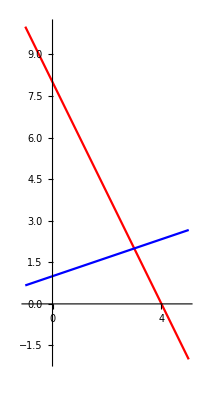

-4<x<2

```mathematica
Solve[x^2+2x-8==0,x]
Solve[{2x+y-8==0,x-3y+3==0}, {x,y}]
Plot[{-2 x + 8, (x + 3)/3}, {x, -1, 5}, PlotStyle → {Red, Blue}, AspectRatio->Automatic]
Reduce[x^2+2x-8<0,x]
```

## Vektorji in matrike

Vektorje pišemo kot sezname v zavitih oklepajih, npr. {3,2,5}. Matrika je seznam seznamov, npr. {{1,2},{3,4}}.
Matriko lahko vnesemo na dva načina:
	- Kot vektor vrstic, kjer je vsaka vrstica vektor.
	- Z menuja Insert Table/Matrix ...

```mathematica
a={1,2,3}
A={{1,2},{3,4}}
A={{1,2},{3,4}}//MatrixForm
```

{1,2,3}

{{1,2},{3,4}}

(1 | 2
3 | 4)

## Definicija funkcije in tabela vrednosti

Mathematica ima seveda vgrajene vse elementarne funkcije. Lahko pa definiramo nove funkcije in le-te uporabljamo tako kot vgrajene funkcije.
Pri definiciji funkcije se je treba natančno držati pisave. Zaporedje znakov  "[x_]:= "  je obvezno.

V Mathematici je običajno, da ukaze gnezdimo.
Vrednosti tabeliramo z ukazom Table[ ].

```mathematica
NovaFun[x_]:=x^3
NovaFun[2]
```

8

```mathematica
Table[NovaFun[k],{k,0,15}]
```

{0,1,8,27,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375}

## Zaporedja, limite, številske vrste

Neenačbe rešujemo z ukazom Reduce[ ]. Za izračun limite uporabimo ukaz Limit[ ]. Vrsto seštejemo z ukazom Sum[ ].

```mathematica
?Reduce
?Limit
?Sum
```

5. Določite monotonost naslednjih zaporedij.
	a) a_n = 1/(n+1)
	b) a_n = n^2
	Rezultati: a) strogo padajoče, b) strogo naraščajoče.

```mathematica
Clear[a,n];
a[n_]:=1/(n+1)
Table[a[n],{n,1,20}]
Reduce[a[n+1]/a[n]<1,n]
Reduce[a[n+1]-a[n]<0,n]
```

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21}

n>-2

```mathematica
b[n_]:=n n
Table[b[n],{n,1,20}]
Reduce[b[n+1]/b[n]>1,n]
Reduce[b[n+1]-b[n]>0,n]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

-1/2<n<0||n>0

n>-1/2

6. Določite omejenost naslednjih zaporedij.
	a) a_n = n/(n+1)
	b) a_n = 2^n/(n!)
	Rezultati: a) min = inf = a_1 = 1/2, max ne obstaja, sup = 1, b) max = sup = a_1 = a_2 = 2, min ne obstaja, inf = 0.

```mathematica
c[n_]:=n/(n+1)
Table[c[n],{n,1,20}] //N
Reduce[c[n+1]-c[n]>0,n]
```

{0.5,0.666667,0.75,0.8,0.833333,0.857143,0.875,0.888889,0.9,0.909091,0.916667,0.923077,0.928571,0.933333,0.9375,0.941176,0.944444,0.947368,0.95,0.952381}

n<-2||n>-1

```mathematica
d[n_]:=2^n/n!
Table[d[n],{n,1,20}] //N
Reduce[d[n+1]/d[n]<=1,n]
```

{2.,2.,1.33333,0.666667,0.266667,0.0888889,0.0253968,0.00634921,0.00141093,0.000282187,0.0000513067,8.55112×10^-6,1.31556×10^-6,1.87937×10^-7,2.50582×10^-8,3.13228×10^-9,3.68503×10^-10,4.09448×10^-11,4.30998×10^-12,4.30998×10^-13}

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

(n!|(1+n)!)∈ℝ&&((Re[n]<-1&&Im[n]==0)||(Re[n]≥1&&Im[n]==0))

7.Izračunajte limitolim_(n→∞) (8 n^2+9n-6)/(2 n^3+3n+1).

```mathematica
Limit[(8n^2+9n-6)/(2n^3+3n+1),n->Infinity]
```

0

8. Izračunajte naslednje limite.
	a) lim_(n→∞) (7 n^2 +  2)/(3 n^2 + 11n - 2) = 7/3
	b) lim_(n→∞)  (√(n+1) - √n) = 0
	c) lim_(n→∞)  ((n+5)/(n+3))^n = ⅇ^2
	d) lim_(n→∞)  (n+3)(log(n+1) - log(n)) = 1

```mathematica
Limit[(7n^2+2)/(3n^2+11n-2), n->Infinity]
Limit[Sqrt[n+1]-Sqrt[n], n->Infinity]
Limit[(((n+5)/(n+3))^n), n->Infinity]
Limit[(n+3)(Log[n+1]-Log[n]), n->Infinity]
```

7/3

0

ⅇ^2

1

9. Ugotovite od katerega člena dalje se vsi členi zaporedja a_n = (n^2 + n)/(n^2+ 1) razlikujejo od limite za manj kot 1/10.
	Rezultat: n_0 = 9.

```mathematica
an=(n^2+n)/(n^2+1); 
a=Limit[an,n->Infinity]; (* *)
eps=1/10;
Reduce[Abs[an-a]<eps,n,Integers]
```

n∈ℤ&&(n≤-11||n==1||n≥9)

10.Izračunajte vsoto geometrijske vrste ∑_(n=1)^∞ 37/100^n.

```mathematica
a = 37/100
q = 1/100
a/(1-q)

Sum[37/100^n,{n,1,Infinity}]
```

37/100

1/100

37/99

37/99

11.Dana je vrsta ∑_(k=1)^∞ a_k  s splošnim členom a_k=1/(9 k^2+3k-2).
   a. Izračunajte n-to delno vsoto s_n=∑_(k=1)^n a_k.
   b. Izračunajte vsoto vrste kot limito zaporedja delnih vsot a=lim_(n→∞) s_n.
   c. Za dan  ϵ=10^-4  poiščite indeks  n_0, za katerega velja  n>n_0  ⟹  |s_n-a|<ϵ.

```mathematica
ak=1/(9k^2+3 k-2); (* splošni člen *)
sn=Sum[ak,{k,1,n}]  (* n-ta vsota *)
(* sn2 = Sum[ak,n -> inf] *)
a=Limit[sn,n->∞]
ϵ=10^-4;
Reduce[Abs[sn-a]<ϵ,n,Integers]
```

n/(2 (2+3 n))

1/6

n∈ℤ&&(n≤-1112||n≥1111)

12. S kvocientnim kriterijem ugotovite, ali je vrsta  ∑ _(n=1)^∞ (n!2^n)/n^n    konvergentna.

```mathematica
Clear[a,n];
a[n_]:=(n!2^n)/n^n
q=Limit[Abs[a[n+1]/a[n]],n->∞]
q//N
N[q]
q<1
If[q<1,Print[konvergentna],
If[q>1,Print[divergentna],
Print[kriterij odpove]]]
Sum[a[n], {n,1, Infinity}] //N
```

2/ⅇ

0.735759

0.735759

True

konvergentna

12.949

13. Določite konvergenco naslednjih vrst.
a. ∑_(n=1)^∞ 1/(n!)
   b. ∑_(n=1)^∞ 3^(2n+1)/(n 5^n)
    c. ∑_(n=2)^∞ 1/(log(n))
	Rezultati: a. konvergentna, b. divergentna, c. divergentna.

```mathematica
Clear[b,n];
b[n_]:=1/(n!)
qb=Limit[Abs[b[n+1]/b[n]],n->∞]
If[qb<1,Print[konvergentna],
If[qb>1,Print[divergentna],
Print[kriterij odpove]]]
Sum[b[n], {n,1, Infinity}] //N
```

0

konvergentna

1.71828

```mathematica
Clear[c,n];
c[n_]:=(3^ (2n+1))/(n 5^ n)
qc=Limit[Abs[c[n+1]/c[n]],n->∞]
If[qc<1,Print[konvergentna],
If[qc>1,Print[divergentna],
Print[kriterij odpove]]]
Sum[c[n], {n,1, Infinity}] //N
```

9/5

divergentna

Sum::div: Sum does not converge.

ComplexInfinity

```mathematica
Clear[d,n];
d[n_]:=1/Log[n]
qd=Limit[Abs[d[n+1]/d[n]],n->∞]
If[qd<1,Print[konvergentna],
If[qd>1,Print[divergentna],
Print[kriterij odpove]]]
Sum[d[n], {n,2, Infinity}] // N
```

1

kriterij odpove

Sum::div: Sum does not converge.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in n near {n} = {8.16907×10^224}. NIntegrate obtained 1.33384617465364×10^27945 and 1.33384617465364×10^27945 for the integral and error estimates.

1.33384617465364×10^27945

```mathematica
Plot[Log[n]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
Plot[{1/Log[n]},{x,1,5}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{1/Log[n]} {x,1,5}]